{{x→InterpolatingFunction[{{0., 60.}}, <>]}}

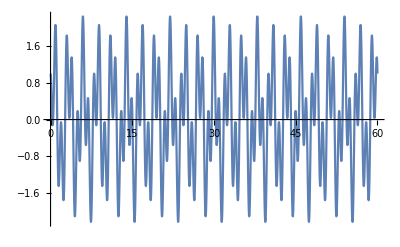

Particle Motion:

```mathematica
m=1;
ω=2Pi;
k=3Pi/4;
v=D[x[t],t];
T=m/2*v^2;
V=m/2*ω^2*(x[t]-Sin[k*t])^2;
ℒ=T-V;
time=60;
Needs["VariationalMethods`"]
eqs=EulerEquations[ℒ,x[t],t];
s=NDSolve[{eqs,x[0]==1,x'[0]==0},x,{t,0,time}]
Plot[Evaluate[x[t]/.s],{t,0,time},PerformanceGoal->"Quality"]

"Particle Motion:"
plt=Plot[-50,{x,-2.2,2.2},PlotRange->{-0.1,0.1},PerformanceGoal->"Quality",Axes->{True,False},AxesStyle->{Directive[0.1,Black],Directive[0,Black]},Ticks->None];
Animate[Show[plt,Graphics[{Blue,Ball[{x[t],0},1/8]}],AspectRatio->Automatic]/.s,{t,0,time},AnimationRate->time/60, AnimationRunning->False,RefreshRate->300]
```

{{r→InterpolatingFunction[{{0., 240.}}, <>],θ→InterpolatingFunction[{{0., 240.}}, <>]}}

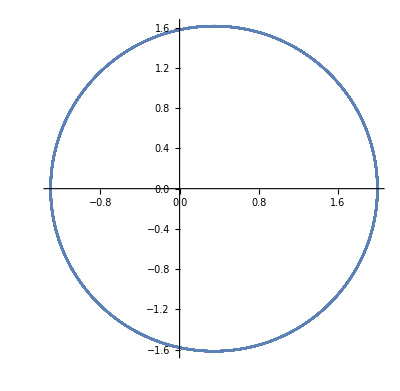

Particle Motion:

```mathematica
m=1;
k=1;
n=-1;
vr=D[r[t],t];
vθ=r[t]*D[θ[t],t];
T=m/2*(vr^2+vθ^2);
V=Sign[n]*m*k*r[t]^n;
ℒ=T-V;
time=240;
Needs["VariationalMethods`"]
eqs=EulerEquations[ℒ,{r[t],θ[t]},t];
s2=NDSolve[{eqs,r[0]==2,r'[0]==0,θ[0]==0,θ'[0]==Pi/10},{r,θ},{t,0,time}]
ParametricPlot[{r[t]*Cos[θ[t]],r[t]*Sin[θ[t]]}/.s2,{t,0,time},PlotPoints->30,PerformanceGoal->"Quality"]

"Particle Motion:"
plt2=Plot[-50,{x,-2.2,2.2},PlotRange->{-2.2,2.2},PerformanceGoal->"Quality",Axes->False,Ticks->None];
Animate[Show[plt2,Graphics[{Blue,Ball[{r[t]*Cos[θ[t]],r[t]*Sin[θ[t]]},1/8]}],ParametricPlot[{r[z]*Cos[θ[z]],r[z]*Sin[θ[z]]}/.s2,{z,Max[0,t-time/16],t},PlotPoints->50],Graphics[{Black,Ball[{0,0},1/16]}],AspectRatio->Automatic]/.s2,{t,0.0001,time},AnimationRate->time/60, AnimationRunning->False,RefreshRate->300]
```